## Exp data for Lu163

```mathematica
ClearAll["Global*`"]
```

#### Band π7/2[523] 1/2

```mathematica
energiesND1=Sort[{10314.7,9252.8,8222.8,7246.9,6334.1,5505.1,4760.7,4103.9,3551.9,3123.4,2748.3,2104.4,1485.8,937.4,492.1,210.1}];
spinsND1=Sort[{69/2,65/2,61/2,57/2,53/2,49/2,45/2,41/2,37/2,33/2,29/2,25/2,21/2,17/2,13/2,9/2}];
energiesND1=energiesND1/1000;
```

#### Band π7/2[523] -1/2

```mathematica
energiesND2=Sort[{12866.0,11781.4,10714.9,9709.0,8713.6,7729.3,6790.0,5916.9,5131.8,4431.4,3822.7,3320.8,2925.0,2307.6,1677.4,1115.4,644.7,295.5,195.31}];
spinsND2=Sort[{79/2,75/2,71/2,67/2,63/2,59/2,55/2,51/2,47/2,43/2,35/2,31/2.,27/2,23/2,19/2,15/2,11/2,7/2}];
energiesND2=energiesND2/1000;
```

#### Band π7/2[404] 1/2

```mathematica
energiesND3=Sort[{13198.3,12098.1,10978.4,9916.8,8927.0,8011.1,7174.2,6415.1,5720.1,5057.5,4405.9,3789.9,3245.2,2803.7,1867.7,1282.5,754.8,310.5}];
spinsND3=Sort[{81/2,77/2,73/2,69/2,65/2,61/2,57/2,53/2,49/2,45/2,41/2,37/2,33/2,29/2,252,21/2,17/2,13/2,9/2}];
energiesND3=energiesND3/1000;
```

#### Band π7/2[404] -1/2

```mathematica
energiesND4=Sort[{13746.8,12627.2,11505.4,10428.3,9408.7,8459.4,7584.4,6788.9,6065.3,5387.9,4719.7,4068.3,3483.8,3004.1,2614.6,2139.8,1562.1,1008.2,520.5,124.36}];
spinsND4=Sort[{83/2,79/2,75/2,71/2,67/2,63/2,59/2,55/2,51/2,47/2,43/2,39/2,35/2,31/2,19/2,15/2,11/2,7/2}];
energiesND4=energiesND4/1000;
```

#### TSD1

```mathematica
energiesTSD1=Sort[{18262,16958,15689,14462.3,13283.0,12156.8,11085.7,10069.2,9106.6,8196.9,7339.1,6533.6,5781.0,5084.0,4445.0,3866.4,3351.1,2900.8,2514.5,2199.6,1936.5,1739.9}];
spinsTSD1=Sort[{97/2,93/2,89/2,85/2,81/2,77/2,73/2,69/2,65/2,61/2,57/2,53/2,49/2,45/2,41/2,37/2,33/2,29/2,25/2,21/2,172,13/2}];
energiesTSD1=energiesTSD1/1000;
```

#### TSD2

```mathematica
energiesTSD2=Sort[{16531,15284,14086.5,12943.5,11854.6,10819.9,9839.7,8913.2,8040.3,7220.4,6454.2,5742.9,5088.3,4492.6,3958.3,3486.6,3079.3}];
spinsTSD2=Sort[{91/2,87/2,83/2,79/2,75/2,71/2,67/2,63/2,59/2,55/2,51/2,47/2,43/2,39/2,35/2,27/2}];
energiesTSD2=energiesTSD2/1000;
```

#### TSD3

```mathematica
energiesTSD3=Sort[{14826,13679.1,12566.7,11503.7,10494.5,9538.7,8636.2,7786.4,6990.5,6249.3,5564.2,4937.2,4369.2,3863.6}];
spinsTSD3=Sort[{91/2,87/2,83/2,79/2,75/2,71/2,67/2,63/2,59/2,55/2,51/2,47/2,43/2,39/2,35/2,31/2,27/2}];
energiesTSD3=energiesTSD3/1000;
```

#### TSD4

```mathematica
energiesTSD4=Sort[{14110,13025.0,11993.4,11017.7,10097.2,9231.8,8421.8,7667.2,6965.0,6319.9}];
spinsTSD4=Sort[{83/2,79/2,75/2,71/2,67/2,63/2,59/2,55/2,51/2,47/2}];
energiesTSD4=energiesTSD4/1000;
```

## Rotational frequencies

Formula for the rotational frequencies taken from Spin determination and calculation of nuclear superdeformed bands in A —190 region, Wu et al.

```mathematica
Egamma[energies_,i_]:=(energies[[i]]-energies[[i-1]]);
rotationalFreqs[energies_]:=Table[Egamma[energies,i]/2,{i,2,Length[energies]}];
dynMOI[energies_]:=Table[4/(Egamma[energies,i+1]-Egamma[energies,i]),{i,2,Length[energies]-1}];
```

```mathematica
rotationalFreqs[energiesND1]
rotationalFreqs[energiesND2]
dynMOI[energiesND1]
dynMOI[energiesND2]
```

{0.141,0.22265,0.2742,0.3093,0.32195,0.18755,0.21425,0.276,0.3284,0.3722,0.4145,0.4564,0.48795,0.515,0.53095}

{0.050095,0.1746,0.23535,0.281,0.3151,0.3087,0.1979,0.25095,0.30435,0.3502,0.39255,0.43655,0.46965,0.49215,0.4977,0.50295,0.53325,0.5423}

{24.4948,38.7973,56.9801,158.103,-14.881,74.9064,32.3887,38.1679,45.6621,47.2813,47.7327,63.3914,73.9372,125.392}

{16.0636,32.9218,43.8116,58.651,-312.5,-18.0505,37.7003,37.4532,43.6205,47.2255,45.4545,60.423,88.8889,360.36,380.952,66.0066,220.994}

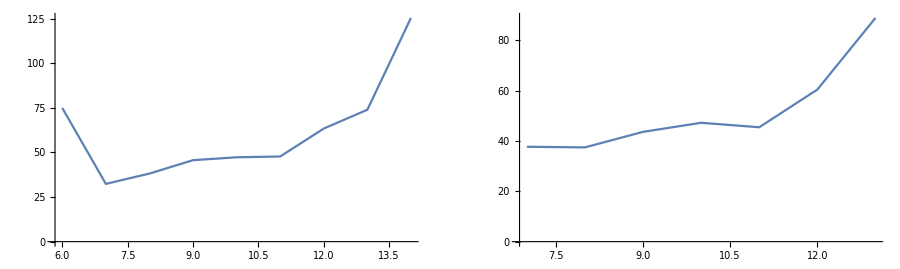

```mathematica
(*ListPlot[Table[{rotationalFreqs[energiesND1][[i+1]],dynMOI[energiesND1][[i]]},{i,1,Length[dynMOI[energiesND1]]}],Joined->True]*)
GraphicsGrid[{{ListPlot[Table[{i,dynMOI[energiesND1][[i]]},{i,6,Length[dynMOI[energiesND1]]}],Joined->True],ListPlot[Table[{i,dynMOI[energiesND2][[i]]},{i,7,Length[dynMOI[energiesND2]]-4}],Joined->True]}},ImageSize->900]
```

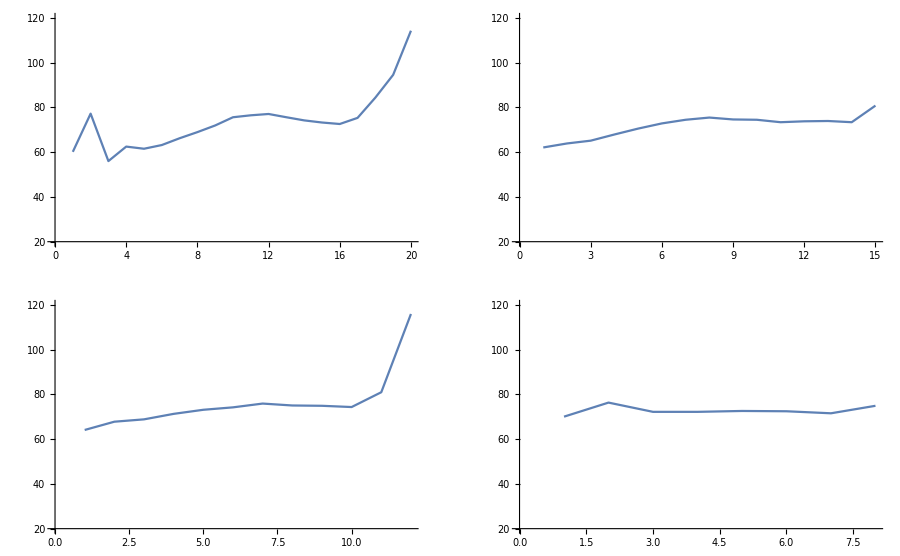

```mathematica
GraphicsGrid[{{ListPlot[Table[dynMOI[energiesTSD1][[i]],{i,1,Length[dynMOI[energiesTSD1]]}],Joined->True,PlotRange->{20,120}],ListPlot[Table[dynMOI[energiesTSD2][[i]],{i,1,Length[dynMOI[energiesTSD2]]}],Joined->True,PlotRange->{20,120}]},{ListPlot[Table[dynMOI[energiesTSD3][[i]],{i,1,Length[dynMOI[energiesTSD3]]}],Joined->True,PlotRange->{20,120}],ListPlot[Table[dynMOI[energiesTSD4][[i]],{i,1,Length[dynMOI[energiesTSD4]]}],Joined->True,PlotRange->{20,120}]}},ImageSize->900]
```